```mathematica
SetDirectory[NotebookDirectory[]];
```

Analytic calculations for the cosmic rays + dark matter subhalos paper

### Notation

- d: distance to center of clump
- r: distance from center of clump to a point
- θ: angle between line-of-site to center of clump and a point
- m: DM mass

### Setup

```mathematica
bLoss[e_]:=b0(e/E0)^2
DDiff[e_]:=D0(e/E0)^δ
λ[eobs_,esource_]:=(D0 E0)/(b0(1-δ))((E0/eobs)^(1-δ)-(E0/esource)^(1-δ))(*HeavisideTheta[esource-eobs]*)
```

```mathematica
ρnfw[r_]:=ρs (rs/r)^γnfw(1+r/rs)^(γnfw-3)
```

Tidally truncated subhalo profile (from Hooper et al)

```mathematica
ρtt[r_]:=ρ0 (Rb/r)^γtt E^(-r/Rb)
```

```mathematica
$Assumptions={r>0,rs>0,ρs>0,ρ0>0,Rb>0,3/2>γtt>0,3/2>γnfw>0};
```

```mathematica
pySubs={ρs->rhos,ρ0->rho0,γtt->gamma,γnfw->gamma,Pi->pi,Sqrt[x_]:>sqrt[x],cθ->cos[th]};
```

```mathematica
pyFormat[expr_]:=expr/.pySubs/.pySubs//FortranForm
```

### Analysis functions

Profile-dependent factor in clump luminosity

```mathematica
Lclump[ρ_]:=Simplify[Integrate[4π r^2 ρ[r]^2,{r,0,∞}]]
```

Computes 𝒦(θ,r,d)=∫ ⅆ(c_θ [ρ(√(d^2+r^2-2d r c_θ))])^2. This is important because:
	J=(2π)/ΔΩ (∫_0)^∞ⅆr [𝒦(0,r,d) - 𝒦(θ_max,r,d)]
	(d^2 ϕ_(e-))/(dE dr)=(π ⟨σv⟩)/(m^2 (b(E) [4π λ(E,m)])^(3/2)) r^2 exp(-r^2/(4λ(E)))[𝒦(0,r,d) - 𝒦(π,r,d)]

```mathematica
𝒦[ρ_]:=Integrate[ρ[√(d^2+r^2-2d r cθ)]^2,cθ]
```

### Results for profiles

#### NFW

```mathematica
Lnfw=Lclump[ρnfw]//FullSimplify;
```

```mathematica
𝒦nfw=𝒦[ρnfw]//FullSimplify;
```

```mathematica
𝒦nfwγ1=𝒦[ρnfw[#]/.γnfw->1&]//FullSimplify;
```

```mathematica
pyFormat[Lnfw]>>"mathematica_to_python/L_clump_nfw.py"
pyFormat[𝒦nfw]>>"mathematica_to_python/K_nfw.py"
pyFormat[𝒦nfwγ1]>>"mathematica_to_python/K_nfw_gamma_1.py"
```

#### TT

```mathematica
Ltt=Lclump[ρtt]//FullSimplify
```

π 2^(2 γtt-1) ρ0^2 Rb^3 3-2 γtt

```mathematica
𝒦tt=𝒦[ρtt]//FullSimplify
```

(4^(γtt-1) ρ0^2 Rb^2 2-2 γtt(2 √(d^2-2 cθ r d+r^2))/Rb)/(d r)

```mathematica
pyFormat[Ltt]>>"mathematica_to_python/L_clump_tt.py"
pyFormat[𝒦tt]>>"mathematica_to_python/K_tt.py"
```

### Distribution over γ_TT

Hooper et al claim that the distribution of γ_TT is independent of the subhalo mass:

```mathematica
prγttSubs={γtt50->0.74,σ->0.42,κ->0.10};
```

```mathematica
prγtt[γ_]:=1/(√(2π))1/(σ-κ(γ-γtt50))Exp[-Log[1-(κ(γ-γtt50))/σ]^2/(2 κ^2)]HeavisideTheta[σ/κ+γtt50-γ]HeavisideTheta[γ]
```

Get quartiles

```mathematica
γtt25=NSolve[N[Integrate[prγtt[γ]/.prγttSubs,{γ,0,γ25},Assumptions->{0<γ25<3/2}]]==0.25,γ25]⟦1⟧⟦1⟧⟦2⟧
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.516816

```mathematica
γtt75=NSolve[N[Integrate[prγtt[γ]/.prγttSubs,{γ,0,γ75},Assumptions->{0<γ75<3/2}]]==0.75,γ75]⟦1⟧⟦1⟧⟦2⟧
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

1.08222

```mathematica
{γtt25,γtt50,γtt75}/.prγttSubs
```

{0.516816,0.74,1.08222}

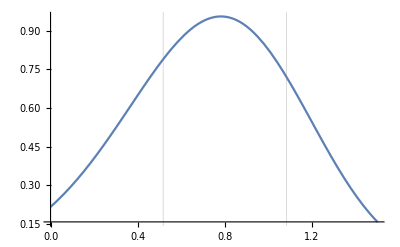

```mathematica
Plot[prγtt[γ]/.prγttSubs,{γ,0,3/2},
GridLines->{{γtt25,γtt75},{}}]
```

### Find velocity distribution

Eddington’s formula relates the phase space distribution function f(ℰ,L) to ρ(r), with f(ℰ,L)=f(ℰ) (where the equality assumes the velocity distribution is isotropic and L is the angular momentum):

	ℰ=ψ-1/2 v^2>0,
	ψ(r)=(∫_r)^r_0 ⅆr' (G m(r'))/(r')^2
	ρ(r)=∫ⅆ^3 v f(ℰ,L)=4π √2(∫_0)^(ψ(r))ⅆℰ f(ℰ)√(ψ(r)-ℰ)
	f_(v⃗)(v⃗,r)=(f(ℰ,L))/(ρ(r))
	f_v(v,r)=v^2∫ ⅆ Ω_v f_(v⃗)(v⃗,r)
	
	f(ℰ)=1/(√8 π^2)d/dℰ(∫_0)^ℰ ⅆψ/(√(ℰ-ψ))dρ/dr=1/(√8 π^2)[1/(√ℰ)dρ/dψ|_(ψ=0)+(∫_0)^ℰ ⅆψ/(√(ℰ-ψ))(d^2 ρ)/dψ^2]

First find ψ

```mathematica
Limit[ψ,rp->∞]//Simplify
```

```mathematica
ψindef=G Integrate[ρnfw[rp]/rp^2,rp]//Simplify;
ψ∞=Limit[ψindef,rp->Infinity];
ψ[r_]:=ψ∞-(ψindef/.rp->r)
```